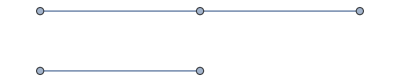

-Graphics-

{}

```mathematica
P1 =Graph[{0<->1,1<->2,3<->4}]
P1a=GraphDisjointUnion[PathGraph[Range[2]],PathGraph[Range[3]]]
FindGraphIsomorphism[P2, P1a]
```

```mathematica
P2 = Graph[{0<->1,1<->2,2<->3,0<->4,3<->4,0<->5,1<->6,2<->7,5<->7,3<->8,5<->8,6<->8,4<->9,6<->9,7<->9}];
FindGraphIsomorphism[P2, PetersenGraph[5,2]]
```

{<|0→1,1→4,2→2,3→7,4→6,5→3,6→9,7→5,8→8,9→10|>}